## Definitions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/stephan_schiffels/dev/celtic_relationship_analysis

```mathematica
CreateDirectory["Figures"]
```

CreateDirectory::eexist: /Users/stephan_schiffels/dev/celtic_relationship_analysis/Figures already exists.

$Failed

```mathematica
readStanDataset[filename_]:=Module[{rawD},
	rawD=Import[filename]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&];
	Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
]
```

```mathematica
hochdorfBurialDateDist=NormalDistribution[-530,6];
aspergBurialDateDist=NormalDistribution[-490,6];
```

```mathematica
hochdorfAgeDist=NormalDistribution[45,6];
aspergAgeDist=NormalDistribution[30,6];
```

```mathematica
mothersAgeDist=NormalDistribution[30,6];
```

## Prior distributions

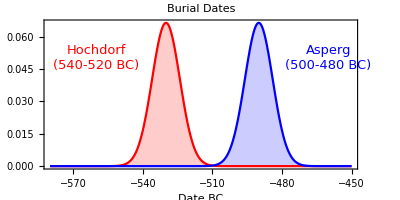

```mathematica
p=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Date BC",None},
Epilog->{
Text[Style["Hochdorf\n(540-520 BC)",Red,13],{-560,0.05}],
Text[Style["Asperg\n(500-480 BC)",Blue,13],{-460,0.05}]
},
PlotLabel->"Burial Dates",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/burialDates.pdf",p]
```

Figures/burialDates.pdf

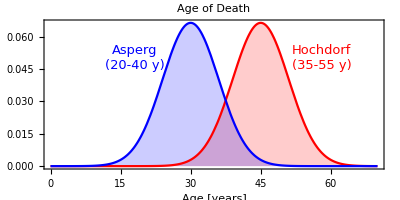

```mathematica
p=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age [years]",None},
Epilog->{
Text[Style["Hochdorf\n(35-55 y)",Red,13],{58,0.05}],
Text[Style["Asperg\n(20-40 y)",Blue,13],{18,0.05}]
},
PlotLabel->"Age of Death",AspectRatio->1/2]
```

```mathematica
Export["Figures/ages.pdf",p]
```

Figures/ages.pdf

```mathematica
n=10000;
hochdorfBirthDateSamples=RandomVariate[hochdorfBurialDateDist,n]-RandomVariate[hochdorfAgeDist,n];
aspergBirthDateSamples=RandomVariate[aspergBurialDateDist,n]-RandomVariate[aspergAgeDist,n];
```

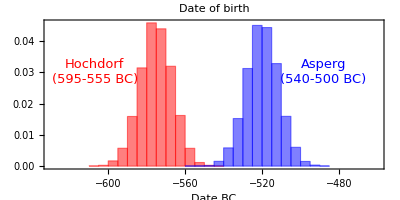

```mathematica
p=Histogram[{hochdorfBirthDateSamples,aspergBirthDateSamples},Automatic,"PDF",PlotRange->{{-630,-460},All},ChartStyle->{Red,Blue},
Frame->{True,False,False,False},
FrameLabel->{"Date BC",None},
Epilog->{
Text[Style["Hochdorf\n(595-555 BC)",Red,13],{-607,0.03}],
Text[Style["Asperg\n(540-500 BC)",Blue,13],{-488,0.03}]
},
PlotLabel->"Date of birth",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/birthDates.pdf",p]
```

Figures/birthDates.pdf

```mathematica
Quantile[hochdorfBirthDateSamples,{0.01,0.99}]
Quantile[aspergBirthDateSamples,{0.01,0.99}]
```

{-594.964,-556.097}

{-539.658,-500.127}

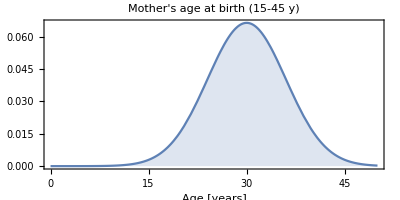

```mathematica
p=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age [years]",None},
PlotLabel->"Mother's age at birth (15-45 y)",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/mothersAge.pdf",p]
```

Figures/mothersAge.pdf

## Maximum likelihood params

### Sibling model

```mathematica
dat=readStanDataset["model_siblings_output.csv"];
```

```mathematica
dat[First,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal
```

<|lp__→-4.15672,accept_stat__→0.933198,stepsize__→0.407607,treedepth__→3,n_leapfrog__→7,divergent__→0,energy__→7.60595,birth_date_mother→-576.249,mother_age_hochdorf→21.6535,mother_age_asperg→39.1657,age_hochdorf→34.6265,age_asperg→38.4911,burial_date_hochdorf→-519.969,burial_date_asperg→-498.592|>

```mathematica
maxLLvalue=
LogLikelihood[NormalDistribution[-530,6],{maxLLparams[["burial_date_hochdorf"]]}]+
LogLikelihood[NormalDistribution[-490,6],{maxLLparams[["burial_date_asperg"]]}]+
LogLikelihood[NormalDistribution[45,6],{maxLLparams[["age_hochdorf"]]}]+
LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_asperg"]]}]+LogLikelihood[NormalDistribution[30,6],{maxLLparams[["mother_age_asperg"]],maxLLparams[["mother_age_hochdorf"]]}]
```

-23.3173

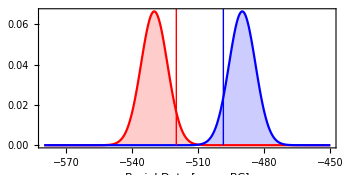

```mathematica
maxLLh=maxLLparams["burial_date_hochdorf"];
maxLLa=maxLLparams["burial_date_asperg"];
p1=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Burial Date [years BC]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

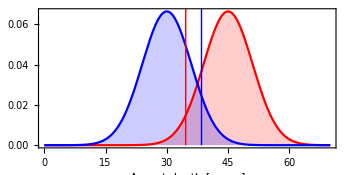

```mathematica
maxLLh=maxLLparams["age_hochdorf"];
maxLLa=maxLLparams["age_asperg"];
p2=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

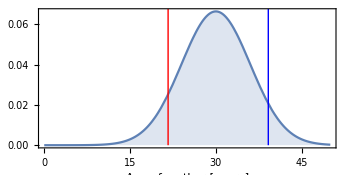

```mathematica
maxLLh=maxLLparams["mother_age_hochdorf"];
maxLLa=maxLLparams["mother_age_asperg"];
p3=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
ImageSize->350
]
```

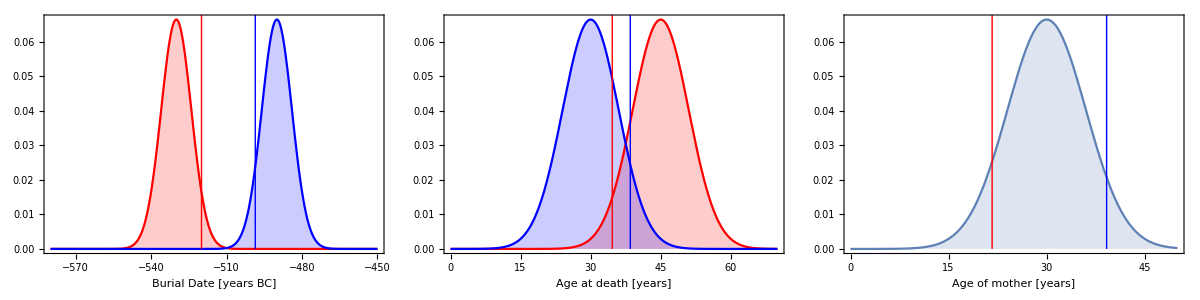

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/sibling_maxLL.pdf",p]
```

Figures/sibling_maxLL.pdf

#### With uncertainty

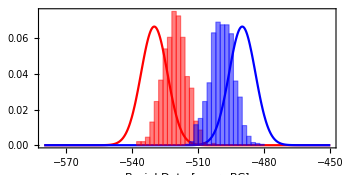

```mathematica
p1=Show[
Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False},
PlotRange->All
],
Histogram[Normal/@{
dat[All,"burial_date_hochdorf"],
dat[All,"burial_date_asperg"]
},Automatic,"PDF",ChartStyle->{Red,Blue}
]
,
FrameLabel->{"Burial Date [years BC]",None},
AspectRatio->1/2,
ImageSize->350
]
```

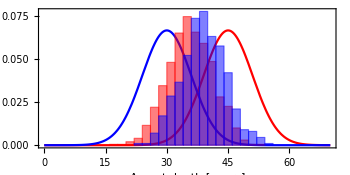

```mathematica
p2=Show[
Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},PlotRange->All
],
Histogram[Normal/@{
dat[All,"age_hochdorf"],
dat[All,"age_asperg"]
},Automatic,"PDF",ChartStyle->{Red,Blue}
],
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
AspectRatio->1/2,
ImageSize->350
]
```

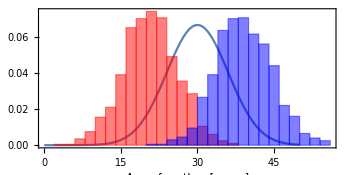

```mathematica
p3=Show[
Plot[PDF[mothersAgeDist,x],{x,0,50}],
Histogram[Normal/@{
dat[All,"mother_age_hochdorf"],
dat[All,"mother_age_asperg"]
},Automatic,"PDF",ChartStyle->{Red,Blue}
],
Frame->{True,False,False,False},
PlotRange->All,
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
ImageSize->350
]
```

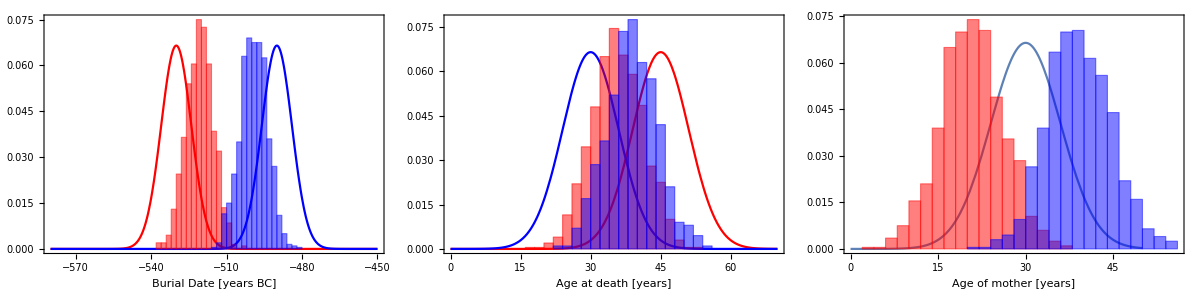

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/sibling_posteriors.pdf",p]
```

Figures/sibling_posteriors.pdf

### Avuncular model

```mathematica
dat=readStanDataset["model_avuncular_output.csv"];
```

```mathematica
dat[First,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_sister,sister_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal
```

<|lp__→19.3623,accept_stat__→0.996511,stepsize__→0.387881,treedepth__→2,n_leapfrog__→7,divergent__→0,energy__→-18.7987,birth_date_mother→-594.706,mother_age_hochdorf→28.39,mother_age_sister→32.9576,sister_age_asperg→35.187,age_hochdorf→42.9703,age_asperg→33.0074,burial_date_hochdorf→-523.345,burial_date_asperg→-493.554|>

```mathematica
maxLLvalue=
LogLikelihood[NormalDistribution[-530,6],{maxLLparams[["burial_date_hochdorf"]]}]+
LogLikelihood[NormalDistribution[-490,6],{maxLLparams[["burial_date_asperg"]]}]+
LogLikelihood[NormalDistribution[45,6],{maxLLparams[["age_hochdorf"]]}]+
LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_asperg"]]}]+LogLikelihood[NormalDistribution[30,6],{maxLLparams[["mother_age_sister"]],maxLLparams[["mother_age_hochdorf"]],maxLLparams[["sister_age_asperg"]]}]
```

-20.4794

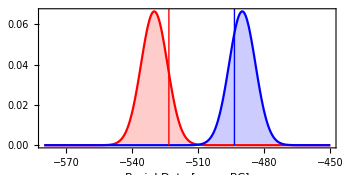

```mathematica
maxLLh=maxLLparams["burial_date_hochdorf"];
maxLLa=maxLLparams["burial_date_asperg"];
p1=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Burial Date [years BC]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

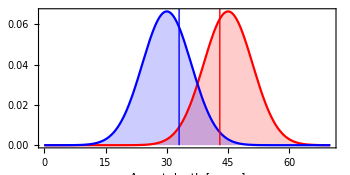

```mathematica
maxLLh=maxLLparams["age_hochdorf"];
maxLLa=maxLLparams["age_asperg"];
p2=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

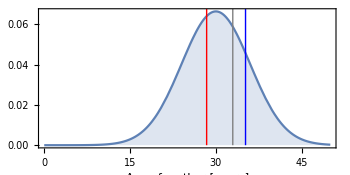

```mathematica
maxLLh=maxLLparams["mother_age_hochdorf"];
maxLLa=maxLLparams["sister_age_asperg"];
maxLLs=maxLLparams["mother_age_sister"];
p3=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}],
Gray,Line[{{maxLLs,0},{maxLLs,1}}]
},
ImageSize->350
]
```

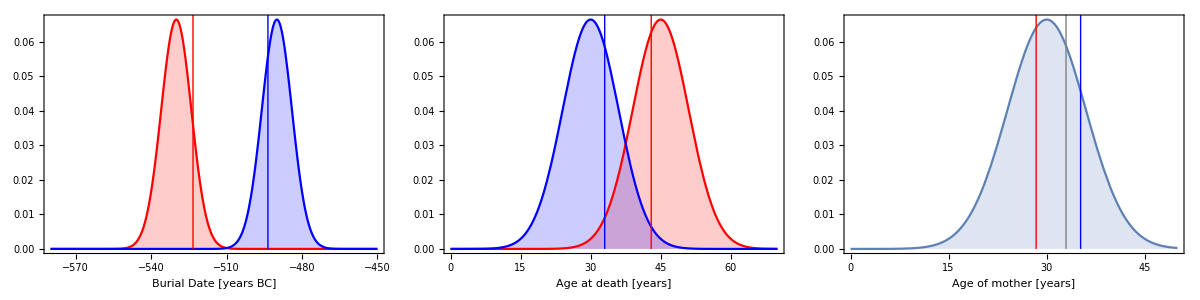

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/avuncular_maxLL.pdf",p]
```

Figures/avuncular_maxLL.pdf

### Cousin model

```mathematica
dat=readStanDataset["model_cousins_output.csv"];
```

```mathematica
dat[First,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_grandmother,grandmother_age_mother_hochdorf,grandmother_age_mother_asperg,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal
```

<|lp__→18.4313,accept_stat__→0.913544,stepsize__→0.373852,treedepth__→3,n_leapfrog__→15,divergent__→0,energy__→-16.3892,birth_date_grandmother→-613.099,grandmother_age_mother_hochdorf→22.8265,grandmother_age_mother_asperg→37.025,mother_age_hochdorf→25.7832,mother_age_asperg→37.3882,age_hochdorf→38.8035,age_asperg→38.5736,burial_date_hochdorf→-525.686,burial_date_asperg→-500.112|>

```mathematica
maxLLvalue=
LogLikelihood[NormalDistribution[-530,6],{maxLLparams[["burial_date_hochdorf"]]}]+
LogLikelihood[NormalDistribution[-490,6],{maxLLparams[["burial_date_asperg"]]}]+
LogLikelihood[NormalDistribution[45,6],{maxLLparams[["age_hochdorf"]]}]+
LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_asperg"]]}]+LogLikelihood[NormalDistribution[30,6],{maxLLparams[["grandmother_age_mother_hochdorf"]],maxLLparams[["grandmother_age_mother_asperg"]],maxLLparams[["mother_age_hochdorf"]],maxLLparams[["mother_age_asperg"]]}]
```

-27.3237

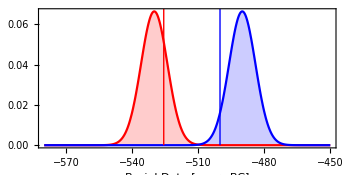

```mathematica
maxLLh=maxLLparams["burial_date_hochdorf"];
maxLLa=maxLLparams["burial_date_asperg"];
p1=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Burial Date [years BC]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

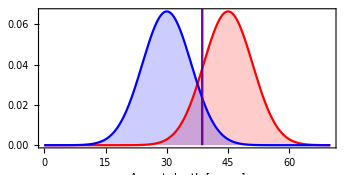

```mathematica
maxLLh=maxLLparams["age_hochdorf"];
maxLLa=maxLLparams["age_asperg"];
p2=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

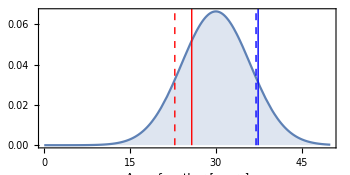

```mathematica
maxLLh1=maxLLparams["grandmother_age_mother_hochdorf"];
maxLLa1=maxLLparams["grandmother_age_mother_asperg"];
maxLLh2=maxLLparams["mother_age_hochdorf"];
maxLLa2=maxLLparams["mother_age_asperg"];
p3=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh2,0},{maxLLh2,1}}],Dashed,Line[{{maxLLh1,0},{maxLLh1,1}}],
Dashing[None],Blue,Line[{{maxLLa2,0},{maxLLa2,1}}],
Dashed,Line[{{maxLLa1,0},{maxLLa1,1}}]
},
ImageSize->350
]
```

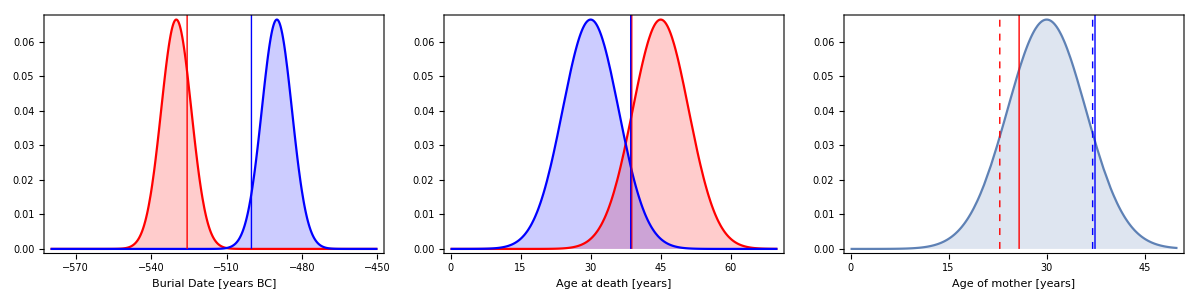

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/cousins_maxLL.pdf",p]
```

Figures/cousins_maxLL.pdf

## Equations

Let L(y|θ) be the likelihood of the data y given parameters θ, and π(θ) be the prior. Then the posterior probability p(θ|y) for parameters θ given data y is

p(θ|y)=(L(y|θ)π(θ))/(∫L(y|θ)π(θ)ⅆθ)=(L(y|θ)π(θ))/M

where we have introduced the “marginal likelihood” M as the normalising constant of the posterior.

### Naive Monte Carlo estimator

For the “Naive Monte Carlo estimator” of M, we produce N prior draws and take the average over the likelihood:

M=∫L(y|θ)π(θ)ⅆθ    =     𝔼_(π(θ))(L(y|θ))    =     1/(N_(prior draws))∑_(i=1)^N L(θ_i)

### Harmonic Mean estimator

We can reorder Bayes Theorem:

p(θ|y)=(L(y|θ)π(θ))/M            ⇒1/M=(p(θ|y))/(L(y|θ)π(θ))

Integrating both sides over the prior:

⇒1/M∫π(θ)ⅆθ=∫(p(θ|y))/(L(y|θ)π(θ))π(θ)ⅆθ=∫1/(L(y|θ))p(θ|y)ⅆθ=𝔼_(p(θ|y))1/(L(y|θ))

so

⇒1/M=𝔼_(p(θ|y))1/(L(y|θ))        ⇒M=(𝔼_(p(θ|y))1/(L(y|θ)))^-1

## Likelihood schema figure

```mathematica
posteriorDist=MultinormalDistribution[{0.5,0.5},{{0.005,0.004},{0.004,0.005}}];
priorDist=ProductDistribution[
UniformDistribution[{0,1}],
UniformDistribution[{0,1}]
];
```

```mathematica
p=Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema.pdf",p]
```

Figures/llFuncSchema.pdf

```mathematica
priorSamples=RandomVariate[priorDist,1000];
```

```mathematica
p=Show[
Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False],
ListPointPlot3D[{#[[1]],#[[2]],PDF[posteriorDist,#[[;;2]]]}&/@priorSamples,PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema2.pdf",p]
```

Figures/llFuncSchema2.pdf

```mathematica
posteriorSamples=RandomVariate[posteriorDist,1000];
```

```mathematica
p=Show[
Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False],
ListPointPlot3D[{#[[1]],#[[2]],PDF[posteriorDist,#[[;;2]]]}&/@posteriorSamples,PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema3.pdf",p]
```

Figures/llFuncSchema3.pdf

```mathematica
points={#[[1]],#[[2]],PDF[posteriorDist,#[[;;2]]]}&/@posteriorSamples;
p=Show[
Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False],
ListPointPlot3D[Select[points,#[[3]]>Median[points[[All,3]]]&],PlotStyle->Red],
ListPointPlot3D[Select[points,#[[3]]<=Median[points[[All,3]]]&],PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema4.pdf",p]
```

Figures/llFuncSchema4.pdf